```mathematica
(* Analysis of population diversity *)
```

```mathematica
(* Bounding function: used to bound the variance of the elements generated within the bounds;  bound=0.6 has been chosen to limit to 1/4 the variance of a random population generated in [0,1] - according to Popoviciu's inequality of variances of bounded probability distributions *)
```

```mathematica
bound=0.6; B[u_]:=If[u≤bound,u,bound]
```

```mathematica
(* Scaling coefficient in the linear function describing the relationship between the variance of the population obtained after mutation and correction and the variance of the current population (pm=mutation probability, pv=violation probability, F=scale factor, m=population size) *)
```

```mathematica
c[pm_,pv_,m_,F_]:=(1-pm)^2+pm*pv*(1-pm)*(m-1)/m+pm^2*(1-pv)^2*B[(m-1)/m+2*F^2]+2*pm*(1-pm)*B[(m-1)/m+F^2]+
2pm^2*pv*(1-pv)*B[(m-1)^2/(2*m^2)+(m-1)/m*F^2]
```

```mathematica
(* Free term in the linear function describing the relationship between the variance of the population obtained after mutation and correction and the variance of the current population (pm=mutation probability, pv=violation probability, F=scale factor, m=population size, Xbar = mean of the current population, Rmean=mean of the corrected elements, Rvar=variance of the corrected elements)*)
```

```mathematica
d[pm_,pv_,m_,F_,Xbar_,Rmean_,Rvar_]:=pm*pv*(1-pm*pv)*(m-1)/m*(Xbar-Rmean)^2+pm*pv*(1-(1-pm*pv)/m)*Rvar
```

```mathematica
(* computation of the mutation probability, depending on the crossover type (CR = crossover rate, n=problem size *)
```

```mathematica
pmBin[CR_,n_]:=CR*(1-1/n)+1/n;  pmExp[CR_,n_]:=(1-CR^n)/(n*(1-CR))
```

```mathematica
(* computation of the variance over generations *)
```

```mathematica
(* Assumption: constant violation probability (pv=F/3) *)
```

```mathematica
lvar[pm_,pv_,m_,F_,Xbar_,Rmean_,Rvar_,varInit_,gen_]:=Module[{var={varInit}},Do[var=Append[var,c[pm,pv,m,F]*Last[var]+d[pm,pv,m,F,Xbar,Rmean,Rvar]],{gen}]; Return[var]]
```

```mathematica
(* Particular case:  saturate;  the violation probability changes in time: pv(g+1)=pv(g)/2+(1-pv(g))(pv(g)^2F/2+(1-pv(g)^2)F/3) *)
```

```mathematica
lvarSaturate[pm_,pv_,m_,F_,Xbar_,Rmean_,Rvar_,varInit_,gen_]:=Module[{var={varInit},Fsat={F/3}},Do[Fsat=Append[Fsat,Last[Fsat]/2+(1-Last[Fsat])*(Last[Fsat]^2*F/2+(1-Last[Fsat]^2)*F/3)];var=Append[var,c[pm,Last[Fsat],m,F]*Last[var]+d[pm,Last[Fsat],m,F,Xbar,Rmean,Rvar]],{gen}]; Return[var]]
```

```mathematica
(* list of values for F and CR *)
```

```mathematica
listF={0.05,0.285,0.52,0.755,0.99}; listCR={0.05,0.285,0.52,0.755,0.99};
```

```mathematica
(* Violation probabilities ajusted based on empirical estimations (in order to compensate for errors induced by the assumption of uniform distribution used in theoretical analysis) *)
```

```mathematica
pvEmp=Reverse[{{F->0.99, pmir-> F/3,  pCOTN-> 0.97*pmir,  pUni-> 0.94*pmir},{F-> 0.755, pmir-> F/3, pCOTN-> 0.92*pmir, pUni-> 0.88*pmir},{F-> 0.52, pmir-> F/3, pCOTN-> 0.79*pmir,  pUni-> 0.75*pmir},{F->0.285,pmir-> F/3,  pCOTN-> 0.58*pmir, pUni-> 0.58*pmir},{F->0.05,pmir-> F/3,  pCOTN-> 0.48*pmir, pUni-> 0.48*pmir}}];
```

```mathematica
(* Computation of the standard deviation over generations for uniform resampling, saturate, mirror and COTN. Assumptions: n=30, m=100, 100 generations,binomial crossover *)
```

```mathematica
n=30; m=100; gen = 100;
```

```mathematica
(* Uniform resampling:  Rmean=Xbar=1/2, Rvar=1/12; a=0, b=1; constant violation probability = F/3 *)
```

```mathematica
Xbar=0.5; Rmean=0.5; Rvar=1.0/12; varinit=1.0/12;stdevUnif=Table[Sqrt[lvar[pmBin[listCR[[indCR]],n],(*listF[[indF]]/3*)pUni/.pvEmp[[indF]]/.pvEmp[[indF]]/.pvEmp[[indF]],m,listF[[indF]],Xbar,Rmean,Rvar,varinit,gen]],{indF,1,Length[listF]},{indCR,1,Length[listCR]}];
```

```mathematica
(* Saturate: Rmean=Xbar=1/2, Rvar=1/4; a=0, b=1; *)
```

```mathematica
Xbar=0.5; Rmean=0.5; Rvar=1.0/4; varinit=1.0/12;
stdevSaturate=Table[Sqrt[lvarSaturate[pmBin[listCR[[indCR]],n],listF[[indF]]/3,m,listF[[indF]],Xbar,Rmean,Rvar,varinit,gen]],{indF,1,Length[listF]},{indCR,1,Length[listCR]}];
```

```mathematica
(* Mirror: Rmean=Xbar=1/2, Rvar = F^2/10-F/4+1/4; a=0, b=1; *)
```

```mathematica
Xbar=0.5; Rmean=0.5;RvarMirror[F_]:=F^2/10-F/4+1/4 ; varinit=1.0/12;stdevMirror=Table[Sqrt[lvar[pmBin[listCR[[indCR]],n],listF[[indF]]/3,m,listF[[indF]],Xbar,Rmean,RvarMirror[listF[[indF]]],varinit,gen]],{indF,1,Length[listF]},{indCR,1,Length[listCR]}];
```

```mathematica
(* COTN: Rmean=Xbar=1/2, Remark: the variance of  corrected elements population is computed considering that this population is a mixture of elements corrected using the lower bound rule and elements corrected using the upper bound rule; Additional assumption: same probability to violate the lower and the upper bound *)
VarLowerCotn[a_,b_,s_]:=(1-2/Pi)*s^2; VarUpperCotn[a_,b_,s_]:=(1-2/Pi)*s^2; MeanLowerCotn[a_,b_,s_]:=a+s*Sqrt[2/Pi]; MeanUpperCotn[a_,b_,s_]:=b-s*Sqrt[2/Pi]; VarCotn[a_,b_,s_]:=(VarLowerCotn[a,b,s]+VarUpperCotn[a,b,s])/2+(MeanLowerCotn[a,b,s]^2+MeanUpperCotn[a,b,s]^2)/2-(MeanLowerCotn[a,b,s]+MeanUpperCotn[a,b,s])^2/4
```

```mathematica
VarCotnWeights[a_,b_,s_,pLB_,pUB_]:= (pLB*VarLowerCotn[a,b,s]+pUB*VarUpperCotn[a,b,s])+(pLB*MeanLowerCotn[a,b,s]^2+pUB*MeanUpperCotn[a,b,s]^2)-(pLB*MeanLowerCotn[a,b,s]+pUB*MeanUpperCotn[a,b,s])^2
```

```mathematica
Simplify[VarCotnWeights[a,b,(b-a)/3,p,1-p]]/.{p->1/2}
```

```mathematica
Simplify[-((a-b)^2 (2-π+1/4 (8+9 π-12 √(2 π))+1/2 (-8-9 π+12 √(2 π))))/(9 π)]
```

((a-b)^2 (13 π-12 √(2 π)))/(36 π)

```mathematica
N[(13-12*Sqrt[2/Pi])/36]
```

0.0951496

```mathematica
(*  Mean of corrected elements - lower bound violation *)
```

```mathematica
fCOTNlb[v_,a_,s_]:=2/(s*Sqrt[2*Pi])*Exp[-(v-a)^2/(2*s^2)]
```

```mathematica
Simplify[Integrate[v*fCOTNlb[v,a,s],{v,a,Infinity}]]
```

ConditionalExpression[(√(2/π)+a √(1/s^2)) s, (Re[a/s^2]<0||Re[s^2]>0)&&Re[s^2]≥0]

```mathematica
(*  Variance of corrected elements - lower bound violation *)
```

```mathematica
Simplify[Integrate[(v-(a+s*Sqrt[2/Pi]))^2*fCOTNlb[v,a,s],{v,a,Infinity}]]
```

ConditionalExpression[(√(1/s^2) s^3 (2+π-4 √(1/s^2) s))/π, Re[s^2]>0]

```mathematica
(*  Mean of corrected elements - upper bound violation *)
```

```mathematica
fCOTNub[v_,b_,s_]:=2/(s*Sqrt[2*Pi])*Exp[-(v-b)^2/(2*s^2)]
```

```mathematica
Simplify[Integrate[v*fCOTNub[v,b,s],{v,-Infinity,b}]]
```

ConditionalExpression[(-√(2/π)+b √(1/s^2)) s, (Re[b/s^2]<0||Re[s^2]>0)&&Re[s^2]≥0]

```mathematica
(*  Variance of corrected elements - upper bound violation *)
```

```mathematica
Simplify[Integrate[(v-(b-s*Sqrt[2/Pi]))^2*fCOTNub[v,b,s],{v,-Infinity,b}]]
```

ConditionalExpression[(√(1/s^2) s^3 (2+π-4 √(1/s^2) s))/π, (Re[b/s^2]<0||Re[s^2]>0)&&Re[s^2]≥0]

```mathematica
(* Standard deviation of the population over generations *)
```

```mathematica
a=0;b=1;Xbar=(a+b)/2; Rmean=(a+b)/2; Rvar=VarCotn[a,b,(b-a)/3]; varinit=(b-a)^2/12;
stdevCOTN=Table[Sqrt[lvar[pmBin[listCR[[indCR]],n], pCOTN/.pvEmp[[indF]]/.pvEmp[[indF]]/.pvEmp[[indF]],m,listF[[indF]],Xbar,Rmean,Rvar,varinit,gen]],{indF,1,Length[listF]},{indCR,1,Length[listCR]}];
```

```mathematica
(* color codes *)
```

```mathematica
colors={{0.4,0.7607843137254902,0.6470588235294118},{0.9882352941176471,0.5529411764705883,0.3843137254901961},{0.5529411764705883,0.6274509803921569,0.796078431372549},{0.9058823529411765,0.5411764705882353,0.7647058823529411},{0.6509803921568628,0.8470588235294118,0.32941176470588235},{0.8980392156862745,0.7686274509803922,0.5803921568627451}};
```

```mathematica
(* Standard deviation of the population after correction (includes both corrected and feasible mutants *)
```

```mathematica
gFCR=Table[Which[indCR==1&&indF==1,ListLinePlot[{stdevSaturate[[indF,indCR]],stdevMirror[[indF,indCR]], stdevCOTN[[indF,indCR]],stdevUnif[[indF,indCR]]}, PlotStyle->{RGBColor[colors[[3]]],RGBColor[colors[[2]]],RGBColor[colors[[1]]],RGBColor[colors[[5]]]},PlotRange->{{0,gen},{0,0.55}},PlotLegends->{Placed[{Text[Style["sat",FontSize->9]],Text[Style["mir",FontSize->9]],Text[Style["COTN",FontSize->9]],Text[Style["uni",FontSize->9]]},{Right,Top}]},Frame->True, FrameLabel->{StringJoin["CR=",ToString[listCR[[indCR]]]],StringJoin["F=",ToString[listF[[indF]]]]},FrameTicksStyle->Directive[Gray,8]],
indCR==1&& indF≠1,ListLinePlot[{stdevSaturate[[indF,indCR]],stdevMirror[[indF,indCR]], stdevCOTN[[indF,indCR]],stdevUnif[[indF,indCR]]}, PlotStyle->{RGBColor[colors[[3]]],RGBColor[colors[[2]]],RGBColor[colors[[1]]],RGBColor[colors[[5]]]},PlotRange->{{0,gen},{0,0.55}},Frame->True, FrameLabel->{"",StringJoin["F=",ToString[listCR[[indF]]]]},FrameTicksStyle->Directive[Gray,8]], 
indCR≠1&& indF==1,ListLinePlot[{stdevSaturate[[indF,indCR]],stdevMirror[[indF,indCR]], stdevCOTN[[indF,indCR]],stdevUnif[[indF,indCR]]}, PlotStyle->{RGBColor[colors[[3]]],RGBColor[colors[[2]]],RGBColor[colors[[1]]],RGBColor[colors[[5]]]},PlotRange->{{0,gen},{0,0.55}},Frame->True, FrameLabel->{StringJoin["CR=",ToString[listCR[[indCR]]]],""},FrameTicksStyle->Directive[Gray,8]],
indCR≠1 && indF≠ 1,ListLinePlot[{stdevSaturate[[indF,indCR]],stdevMirror[[indF,indCR]], stdevCOTN[[indF,indCR]],stdevUnif[[indF,indCR]]}, PlotStyle->{RGBColor[colors[[3]]],RGBColor[colors[[2]]],RGBColor[colors[[1]]],RGBColor[colors[[5]]]},PlotRange->{{0,gen},{0,0.55}},Frame->True, FrameLabel->{"",""},FrameTicksStyle->Directive[Gray,7]]],{indF,Length[listF],1,-1},{indCR,1,Length[listCR]}];
```

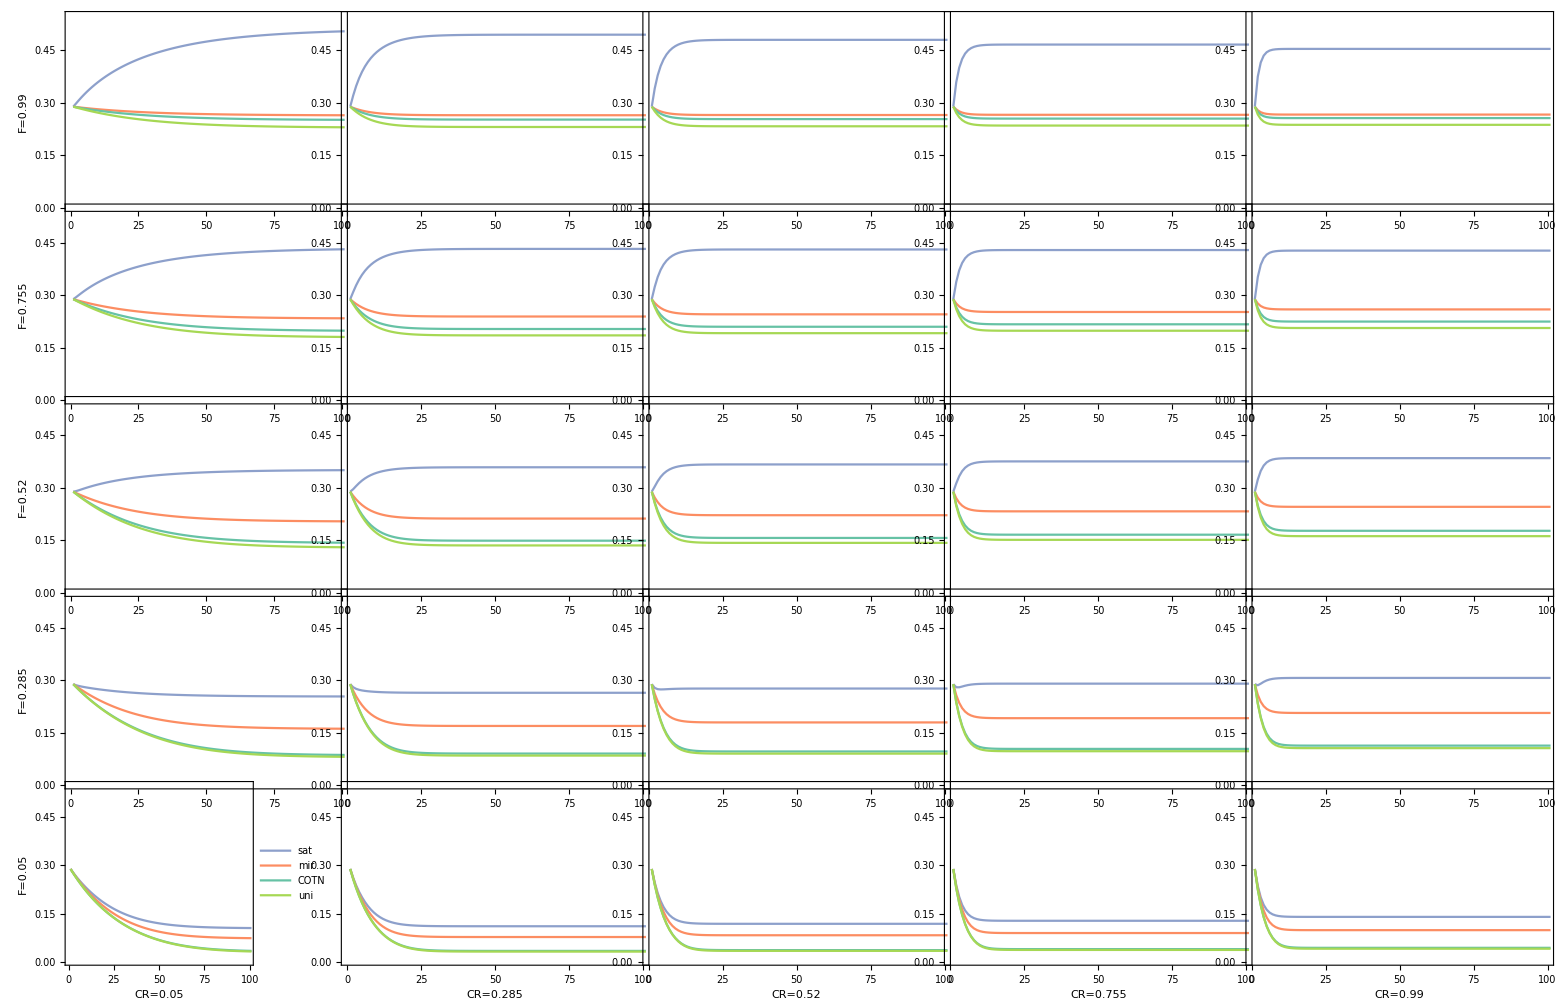

```mathematica
GraphicsGrid[gFCR,Spacings->{Scaled[-0.2],Scaled[-0.2]}]
```

```mathematica
(*  Standard deviation of the corrected elements *)
```

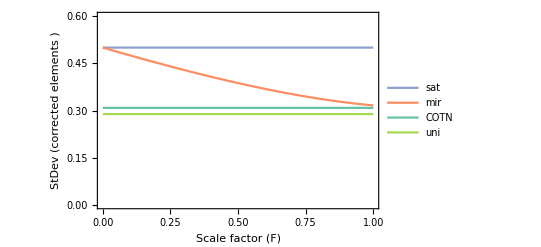

```mathematica
gStDevCor=Plot[{Sqrt[1/4.0],Sqrt[3*F^2/80+F^2/16-F/4+1/4],Sqrt[VarCotn[a,b,(b-a)/3]],Sqrt[1/12.0]},{F,0,1},PlotStyle->{RGBColor[colors[[3]]],RGBColor[colors[[2]]],RGBColor[colors[[1]]],RGBColor[colors[[5]]]},PlotRange->{{0,1},{0,0.6}},Frame->True, FrameLabel->{"Scale factor (F)","StDev (corrected elements )"},PlotLegends->Placed[{"sat","mir","COTN","uni"},{Left,Bottom}]]
```